# Практикум №4. Построение пользовательской функции дифференцирования

Выполнил студент ММФ  БГУ
КМ, 1 к, 3 гр . Шпак А . В .
 23 октября 2021

## 1. Знакомство с принципами построения правил преобразований.

### Задание 1.

Ознакомьтесь с принципами построения пользовательской функции integrate, которая описана в системе справки Mathematica. Для поиска необходимой информации наберите в строке поиска справочной системы tutorial/AnExampleDefiningYourOwnIntegrationFunction.
Комментарии к решению: во время работы возникла маленькая проблема. Возможно это связано с тем, что у меня более поздняя версия Wolfram Mathematica: справочная система отказывалась искать туториал по ссылке tutorial/AnExampleDefiningYourOwnIntegrationFunction. Но я погуглил и нашёл актуальную ссылку на туториал для моей версии: tutorial/Patterns#23271.

```mathematica
(*Знакомство с туториалом.*)
(*Шпаргалка*)
(*{{mathematical form, Wolfram Language definition}, {∫(y+z)ⅆx==∫yⅆx+∫zⅆx, integrate[y_+z_,x_]:=integrate[y,x]+integrate[z,x]}, {∫cyⅆx==c∫yⅆx (c independent of x), integrate[c_y_,x_]:=c integrate[y,x]/;FreeQpaclet:ref/FreeQ[c,x]}, {∫cⅆx==cx, integrate[c_,x_]:=cx/;FreeQpaclet:ref/FreeQ[c,x]}, {∫x^n ⅆx==x^(n+1)/(n+1), n≠-1, integrate[x_^n_.,x_]:=x^(n+1)/(n+1)/;FreeQpaclet:ref/FreeQ[n,x]&&n!=-1}, {∫1/(ax+b)ⅆx==(log(ax+b))/a, integrate[1/(a_.x_+b_.),x_]:=Logpaclet:ref/Log[ax+b]/a/;FreeQpaclet:ref/FreeQ[{a,b},x]}, {∫e^(ax+b)ⅆx==1/a e^(ax+b), integrate[Exppaclet:ref/Exp[a_.x_+b_.],x_]:=Exppaclet:ref/Exp[ax+b]/a/;FreeQpaclet:ref/FreeQ[{a,b},x]}}*)
(*Реализация соотношения линейности для интегралов: ∫(y+z)ⅆx==∫yⅆx+∫zⅆx*)
integrate[y_+z_,x_]:=integrate[y,x]+integrate[z,x]
(*Ассоциативность Plus заставляет отношение линейности работать с любым количеством членов в сумме*)
integrate[a x+b x^2+3,x]
integrate[2+3+13+x+13Log[x],x]
```

3 x+(a x^2)/2+(b x^3)/3

18 x+x^2/2+13 integrate[Log[x],x]

```mathematica
(*Описываю случай произведения константы на подынтегральное выражение. Использую операторную форму функции Condition (/;), то есть условие будет выполняться, если правая часть вернёт true. А функция FreeQ проверяет, действительно ли в наличии у меня константа, сравнивая каждое подвыражение c с x, возвращает true, если совпадений не найдено*)
integrate[c_ y_,x_]:=c integrate[y,x]/;FreeQ[c,x]
integrate[a x+b x^2+3,x]
integrate[3 x^3+5 x^13+x+4+43 x^2,x]
```

3 x+(a x^2)/2+(b x^3)/3

4 x+x^2/2+(43 x^3)/3+(3 x^4)/4+(5 x^14)/14

```mathematica
(*Описываю в функции следующий частный случай, когда в пдынтегральном выражении находится только константа: ∫cⅆx==cx*)
integrate[c_,x_]:=c x/;FreeQ[c,x]
integrate[a x+b x^2+3,x]
integrate[3 x^3+5 x^13+x+4+43 x^2,x]
```

3 x+(a x^2)/2+(b x^3)/3

4 x+x^2/2+(43 x^3)/3+(3 x^4)/4+(5 x^14)/14

```mathematica
(*Описываю стандартную формулу интеграла из x^n. Использую паттерн _., чтобы была возможность использовать встроенные значения по умолчанию.*)
integrate[x_^n_.,x_]:=x^(n+1)/(n+1)/;FreeQ[n,x]&&n!=-1
(*Теперь я полностью могу посчитать следующий интеграл*)
integrate[a x+b x^2+3,x]
integrate[5 x+11x^2-5,x]
(*И сравнить с функцией из Mathematica*)
Integrate[a x+b x^2+3,x]
Integrate[5 x+11x^2-5,x]
```

3 x+(a x^2)/2+(b x^3)/3

-5 x+(5 x^2)/2+(11 x^3)/3

3 x+(a x^2)/2+(b x^3)/3

-5 x+(5 x^2)/2+(11 x^3)/3

```mathematica
(*Правило интегрирования обратной линейной функции ∫1/(ax+b)ⅆx==(log(ax+b))/a. Шаблон a_.x_+b_. тспользуется для любой линейной функции x*)
```

```mathematica
integrate[1/(a_. x_+b_.),x_]:=Log[a x+b]/a/;FreeQ[{a,b},x]
integrate[1/x,x]
integrate[1/(2 p x-1),x]
```

Log[x]

Log[-1+2 p x]/(2 p)

```mathematica
(*Можно добавлять другие правила, чтобы дополнять свою функцию, например ∫e^(ax+b)ⅆx==1/a e^(ax+b)*)
integrate[Exp[a_. x_+b_.],x_]:=Exp[a x+b]/a/;FreeQ[{a,b},x]
```

```mathematica
?integrate
(*RuleDelayed (:>) представляет правило, которое преобразует левую часть выражения в правую,вычисляя правую только в процессе использования правила*)
DownValues[integrate]
```

{HoldPattern[integrate[y_+z_,x_]]:>integrate[y,x]+integrate[z,x],HoldPattern[integrate[c_ y_,x_]]:>c integrate[y,x]/;FreeQ[c,x],HoldPattern[integrate[c_,x_]]:>c x/;FreeQ[c,x],HoldPattern[integrate[x_^(n_.),x_]]:>x^(n+1)/(n+1)/;FreeQ[n,x]&&n≠-1,HoldPattern[integrate[1/(b_.+a_. x_),x_]]:>Log[a x+b]/a/;FreeQ[{a,b},x],HoldPattern[integrate[ⅇ^(b_.+a_. x_),x_]]:>Exp[a x+b]/a/;FreeQ[{a,b},x]}

## 2. Основные правила дифференцирования функции одной переменной.

### Задание 2.

Определите основные правила дифференцирования функции одной переменной, закрепив их за символом Dif. Проверьте, как работают правила. Сформулируйте необходимые объяснения по ходу выполнения задания.

```mathematica
(*Основные правила дифференцирования:*)
(*Очищаю все значения, аттрибуты, сообщения и значения по умолчанию, ассоциированые с символом Dif*)
ClearAll[Dif]
(*Описываю правило дифференцирования для одной переменной x:*)
Dif[x_,x_Symbol]=1;
(*Правило для производной от суммы, равной сумме производных:*)
Dif[u_+v_,x_Symbol]:=Dif[u,x]+Dif[v,x]
(*Правило для производная от произведения, равной сумме произведений первого множителя на производную второй и второго множителя на производную первого:*)
Dif[u_ v_,x_Symbol]:=Dif[u,x]v+u Dif[v,x]
(*Проверяю:*)
Dif[x,x]
Dif[14,x]
Dif[3x,x]
Dif[3x+5x,x]
Dif[3x+5x+8x+17x+22, x]
Dif[0,x]
Dif[3x 5x,x]
Dif[3x 5 x^2,x]
Dif[3x 5 x^2 8 x^3 (x+1)^2,x]
```

1

Dif[14,x]

3+x Dif[3,x]

8+x Dif[8,x]

33+Dif[22,x]+x Dif[33,x]

Dif[0,x]

x^2 Dif[15,x]+15 Dif[x^2,x]

x^3 Dif[15,x]+15 Dif[x^3,x]

x^6 (1+x)^2 Dif[120,x]+120 ((1+x)^2 Dif[x^6,x]+x^6 Dif[(1+x)^2,x])

```mathematica
(*Проверяю с помощью Definition глобальные правила:*)
?Dif
(*Пример из учебника:*)
Dif[7-6x+5 x^2-4 xy^3+Sin[3 x^2]-(9x+a)/(8b-10x),x]
(*Пока что моя функция Dif не "обучена" дифференцированию константы, синусы, переменной в степени или более сложной функции. Исправлю это в будущем*)
```

-6+x Dif[-6,x]+xy^3 Dif[-4,x]+((a+9 x) Dif[-1,x])/(8 b-10 x)+x^2 Dif[5,x]+Dif[7,x]-(9+x Dif[9,x]+Dif[a,x])/(8 b-10 x)-(a+9 x) Dif[1/(8 b-10 x),x]+5 Dif[x^2,x]-4 Dif[xy^3,x]+Dif[Sin[3 x^2],x]

```mathematica
(*Почему при дифференцировании суммы с количеством слагаемых более двух Mathematica сама "догадалась" использовать правило, хотя мы ей это явно не указали? Воспользуюсь подскаской, использую функцию Trace:*)
Trace[Dif[as+ad+af,x]]
```

{{as+ad+af,ad+af+as},Dif[ad+af+as,x],Dif[ad,x]+Dif[af+as,x],{Dif[af+as,x],Dif[af,x]+Dif[as,x]},Dif[ad,x]+(Dif[af,x]+Dif[as,x]),Dif[ad,x]+Dif[af,x]+Dif[as,x]}

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
(*Атрибуты: Orderless - выражение должно быть отсортировано, представлено в правильном порядке. Protected - предотвращает изменение любых значений,связанных с символом. Listable - позволяет работать со списками, элементами списков, производя операцию с соответствующими элементами каждго из списков; наделяет функцию свойством дистрибутивности относительно списков. Функция, имеющая этот атрибут, действует на каждый аргумент списка, в результате возвращается список. Атрибут Flat соответствует свойству ассоциативности операции.*)(*Вопрос: правильно ли я понял, почему Mathematica "догадалась" использовать правило для дифференцировании суммы с количеством слагаемых более двух? Проанализировав выполнение Trace, я предполагаю, что, благодаря тому, что Plus обладает свойствами ассоциативности и коммутативности, функция "смотрит" на сумму как на два выражения, сначала берёт первый аргумент, а затем уже в виде второго аргумента то количество слагаемых, которое осталось, и так по цепочке.
*)
(*Так моя функция вычисляет некоторое выражение*)
Dif[4x y^3,x]
(*Переопределяю правило дифференцирования произведения, чтобы, чтобы обучить функцию раскрывать скобки после произведения*)
Dif[u_ v_,x_Symbol]:=Dif[u,x]v+u Dif[v,x]//Expand
?Dif
Dif[4x y^3,x]
```

x y^3 Dif[4,x]+4 (y^3+x Dif[y^3,x])

4 y^3+x y^3 Dif[4,x]+4 x Dif[y^3,x]

```mathematica
(*Поговорим про производную частного. Почему Mathematica умеет её вычислять несмотря на отсутсвие правила?*)
Dif[(9x+a)/(8b-10x),x]
(*На самом деле она её и не вычисляет. Мы не описывали соответствующее правило. А говоря о частном вида f/g, я предполагаю, что оно рассматривается системой как Times[f,1/g] или f*(1/g), то есть как произведение, соотвутствующе и вычисляется*)
(*Другие примеры:*)
Dif[13Tan[Pi x],x]
Dif[(11 x^3)/(5+x),x]
Dif[Log[11]+15 Sin[Pi/3 x]^2-23,x]
```

9/(8 b-10 x)+(x Dif[9,x])/(8 b-10 x)+Dif[a,x]/(8 b-10 x)+a Dif[1/(8 b-10 x),x]+9 x Dif[1/(8 b-10 x),x]

13 Dif[Tan[π x],x]+Dif[13,x] Tan[π x]

(x^3 Dif[11,x])/(5+x)+(11 Dif[x^3,x])/(5+x)+11 x^3 Dif[1/(5+x),x]

Dif[-23,x]+Dif[Log[11],x]+15 Dif[Sin[(π x)/3]^2,x]+Dif[15,x] Sin[(π x)/3]^2

## 3. Производные основных элементарных функций.

### Задание 3.

Для функции Dif[expr,x] определите правила дифференцирования основных элементарных функций.

```mathematica
(*Перед выполнением задания 3 сделаю два подзадания: попробую ввести в использование компактное обозначение производной и, более важное, описать производную сложной функции.*)
(*3.0.1*)
(*Представляю операцию диффуренцирования в традиционной математической нотации. Для этого переопределяю выходной формат выражения Dif[expr,x]:*)
(*Вопрос:выражение снизу сейчас вызывает у меня трудности, я бы хотел или разобрать его подробней или, если так просто с ним не справиться, узнать, будем ли мы это ещё в будущем рассматривать на лекциях. Или, если всё просто, может мне стоит внимательней прочитать литературу. В любом случае, чтобы не тратить время зря.*)
Dif/:MakeBoxes[Dif[expr_,x_],form_]:=SubsuperscriptBox[RowBox[{"(",MakeBoxes[expr,form],")"}],ToString[x],"'"]
(*Проверяю:*)
Dif[13-12x+11 x^2-2 xy^3+Sin[2 x^2]-(3x+a)/(2b-4x),x]
(*Разбираюсь, что произошло:*)
(*TagSetDelayed (/:) - предназначен для того, чтобы связать символ Dif с выражением SubsuperscriptBox... *)
(*MakeBoxes - функция, предназначенная для конвертации выражений в боксы.*)
(*SubsuperscriptBox["x","y","z"] - функция для отображения выражений вида Subscript[x, y]^z*)
(*Примеры:*)
MakeBoxes[a+b^2,StandardForm]
SubsuperscriptBox[5,i,3]//DisplayForm
```

-12-3/(2 b-4 x)+x ((-12)')_x+xy^3 ((-2)')_x+(a ((-1)')_x)/(2 b-4 x)+(3 x ((-1)')_x)/(2 b-4 x)-(x ((3)')_x)/(2 b-4 x)+x^2 ((11)')_x+((13)')_x-(((a)')_x)/(2 b-4 x)-a ((1/(2 b-4 x))')_x-3 x ((1/(2 b-4 x))')_x+11 ((x^2)')_x-2 ((xy^3)')_x+((Sin[2 x^2])')_x

RowBox[{a,+,SuperscriptBox[b,2]}]

5_i^3

```mathematica
Plus[a,b]^:=4
a+b
?a
UpValues[a]
?b
```

4

{HoldPattern[a+b]:>4}

```mathematica
Derivative
f[x_] := Sin[x] + x^2
g'[x]//FullForm
```

Derivative

```mathematica
Derivative[3][g]=2
SubValues[Derivative]
```

Cos[1+x]

Cos[1-x]

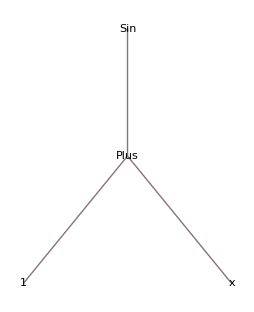

```mathematica
(*3.0.2*)
(*Производная сложной функции:*)
(*Вопрос:хочу прочитать выражение снизу, чтобы убедиться, правильно ли я его понимаю.*)
Dif[f_[expr_],x_Symbol]:=Block[{u},(Dif[f[u],u]/.u->expr)Dif[expr,x]]/;And[FreeQ[f,x],!AtomQ[expr]];
(*Что я делаю:*)
(*Использую Block для введения локальной переменной u*)
(*Использую функцию ReplaceAll для того, чтобы получить новую производную*)
(*Условие, записанное в конце Block спасает функцию от зацикливания тем, что очередное условие перед Condition выполнится только в том случае, когда And[FreeQ[f,x],!AtomQ[expr]] вернёт true, то есть пока expr не атомарное выражение и f не совпадает с x*)
(*Проверяб работу правила:*)
Dif[Sin[x+1],x]
Dif[Sin[x-1],x]
(*Не знаю, почему так.*)
Sin[x+1]//TreeForm
Sin[x-1]//TreeForm
```

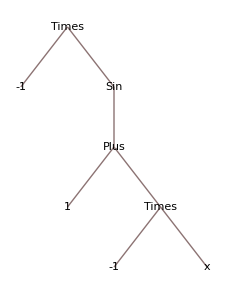

```mathematica
Sin[x-1]//TreeForm
```

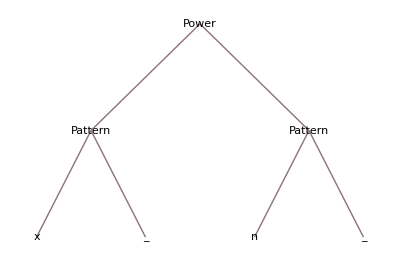

False

```mathematica
x_^n_//TreeForm
MatchQ[c,x_^n_]
```

```mathematica
(*Определяю правила вычисления производных основных элементарных функций:*)
Dif[c_,x_Symbol]:=0/;FreeQ[c,x];
Dif[x_^(n_.),x_Symbol]:=n x^(n-1)/;FreeQ[n,x];
Dif[a_^x_,x_Symbol]:=a^x Log[a]/;FreeQ[a,x];
Dif[Sin[x_],x_Symbol]:=Cos[x];
Dif[Cos[x_],x_Symbol]:=-Sin[x];
Dif[Log[x_],x_Symbol]:=1/x;
(*Главное отличие MemberQ[list,form] от FreeQ[expr,form] в том, что результатом первая функция возвращает true, но в том случае, если элемент из списка как-то совпадает с form;  наших же примерах мы используем FreeQ для того, чтобы точно так же получать результатом true, но только тогда, когда expr и form не совпадают, проводя таким образом проверку на независимость константы от переменной.*)
?Dif
(*^:= ???*)
```

```mathematica
(*Каким образом и где Mathematica хранит всю информацию о символе Dif. Получим список встроенных функций, в имени которых содержится фрагмент Values*)
Names["*Values*"]
(*Вопрос: возникают ошибки*)
(*Column[#->Symbol[#][Dif]&/@%];*)
(*Смотрю списки UpValues и DownValues символа Dif*)
DownValues[Dif]
UpValues[Dif]
(*Объяснение: в процессе ассоциации символа с некоторым правилом происходит его запись в один из списков значений символов: OwnValues, UpValues, DownValues, SubValues*)
(*При вычислении выражений в системе работает механизм правил преобразования:*)
(*Пополнение определённого списка значений символа  - в момент введения глобальных правил*)
(*Обязательный просмотр списков значений того символа, который является частью вычисляемого выражения, и возможное применение некоторого правила из списка - в момент вычисления выражения, которое содержит этот символ.*)
(*Используя функцию SetDelayed, ассоциируя мой символ с некоторым выражением, правило заносится в список DownValues. А, например,используя Set правило заносится в список OwnValues.*)
(*Потому при вызове DownValues[Dif] и UpValues[Dif] в последнем случае на выходе получим пустой список*)
(*Отличие от Information в том, что вызывая конкретно DownValues, мо просматриваем конкретно список правил, заданных с помощью SetDelayed, а Information сама по себе выводит просто список всех правил,которые имеются у Mathematica.*)
(*HoldPattern представляет эквивалент выражения но в определённом, "невычисленном" виде.*)
```

{DefaultValues,DownValues,DynamicModuleValues,FormatValues,NSolveValues,NValues,OwnValues,SingularValues,SolveValues,SubValues,SynthesizeMissingValues,UpValues,Values,ValuesData}

{HoldPattern[((x_)')_x_Symbol]:>1,HoldPattern[((u_+v_)')_x_Symbol]:>((u)')_x+((v)')_x,HoldPattern[((expr1_ expr2_)')_x_Symbol]:>Expand[myDif[expr1,x] expr2+expr1 myDif[expr2,x]],HoldPattern[((f_[expr_])')_x_Symbol]:>Block[{u},(((f[u])')_u/.u→expr) ((expr)')_x]/;FreeQ[f,x]&&!AtomQ[expr],HoldPattern[((c_)')_x_Symbol]:>0/;FreeQ[c,x],HoldPattern[((x_^n_)')_x_Symbol]:>n x^(n-1)/;FreeQ[n,x],HoldPattern[((a_^x_)')_x_Symbol]:>a^x Log[a]/;FreeQ[a,x],HoldPattern[((Sin[x_])')_x_Symbol]:>Cos[x],HoldPattern[((Cos[x_])')_x_Symbol]:>-Sin[x],HoldPattern[((Log[x_])')_x_Symbol]:>1/x,HoldPattern[((c_.)')_x_Symbol]:>0/;FreeQ[c,x]}

{}

```mathematica
(*Проверю выполнение своей функции Dif на примере, предложенном в книге:*)
Dif[12 x^3-23^(3x)+Sin[2x-x^2],x]
```

36 x^2+(2-2 x) Cos[2 x-x^2]-((23^(3 x))')_x

```mathematica
(*Попробую исправить правило для вычисления показательной производной. Для начала сравню полные формы степенного и показательного выражения:*)
(*Вопрос: исправить не получается. Как объдинить правила степенной и показательной функции и как описать корректно, можно ли мне получить подсказку?*)
```

## 4. Вычисление производной функции одной переменной.

### Задание 4.

Тестируйте функцию Dif, вычисляя производные y’ следующих функций  по вариантам. Проверьте правильность вычисления посредством встроенной  функции дифференцирования D. Укажите какие правила необходимы для  вычисления каждого из примеров. Приведите два примера выражения, которые  функция Dif не сможет продифференцировать. Предположите, каких правил  не хватает для вычисления производных.
Вариант 9.

```mathematica
(*Тестирую мою функцию Dif и сравниваю с D:*)
y1=(x^5+1)/(x^4+1)
y2=(x^16+9)/(1-5 x^2)
Dif[y1,x]
Dif[y2,x]
```

(1+x^5)/(1+x^4)

(9+x^16)/(1-5 x^2)

(5 x^4)/(1+x^4)+((1/(1+x^4))')_x+x^5 ((1/(1+x^4))')_x

(16 x^15)/(1-5 x^2)+9 ((1/(1-5 x^2))')_x+x^16 ((1/(1-5 x^2))')_x

```mathematica
(*Не хватает правила для вычисления производной частного:*)
Dif[(u_.)/v_,x_Symbol]:=(Dif[u,x]v-u Dif[v,x])/v^2;
Dif[y1,x]//Simplify
Dif[y2,x]//Simplify
```

(x^3 (-4+5 x+x^5))/((1+x^4)^2)

(90 x+16 x^15-70 x^17)/((1-5 x^2)^2)

```mathematica
(*Сравниваю с встроенной:*)
D[y1,x]//Simplify
D[y2,x]//Simplify
(*Для вычисления каждого из примеров используются следующие правила. Основные стандартные: производная произведения, производная частного, производная суммы. А так же производная переменной в степени, производная константы*)
```

(x^3 (-4+5 x+x^5))/((1+x^4)^2)

(90 x+16 x^15-70 x^17)/((1-5 x^2)^2)

```mathematica
(*Два примера, которые Dif продифференцировать не сможет*)
Dif[x ArcSin[(2x+3)/3],x]
Dif[(ArcTan[2x])^Sin[3x],x]
(*Для вычисления этих производных не хватает правил дифференцирования арксинуса и арктангенса.*)
```

ArcSin[1/3 (3+2 x)]+2/3 x ((ArcSin[1/3 (3+2 x)])')_(3 + 2 x
-------
   3)

((ArcTan[2 x]^Sin[3 x])')_x

## 5. Дифференцирование параметрически заданной функции.

### Задание 5.

Напишите пользовательскую функцию, возвращающую производные функции, заданной параметрически. Найдите производные y’ и y’’ своей функции.
Вариант 9.

```mathematica
(*Очищаю все значения, аттрибуты, сообщения и значения по умолчанию, ассоциированые с символом myDif*)
ClearAll[DifParametric]
(*Правило вычисления первой произвожной*)
DifParametric[xt_,yt_,1]:=D[yt,t]/D[xt,t]//Simplify
(*Правило вычисления n-й производной*)
DifParametric[xt_,yt_,n_Integer?Positive]:=D[DifParametric[xt,yt,n-1],t]/D[xt,t]//FullSimplify
(*Проверяю правила:*)
?DifParametric
```

```mathematica
(*Пробую посчитать свои функции:*)
x1=ArcCos[1/t];
y1=Sqrt[t^2-1]+ArcSin[1/t];
x2=1/Log[Exp,t];
y2=Log[Exp,(1+Sqrt[1-t^2])/t];
DifParametric[x1,y1,1]
DifParametric[x1,y1,2]
DifParametric[x2,y2,1]
DifParametric[x2,y2,2]
```

-1+(√(1-1/t^2) t^3)/(√(-1+t^2))

2 t^2 √(-1+t^2)

Log[t]^2/(√(1-t^2) Log[Exp]^2)

-(Log[t]^3 (2-2 t^2+t^2 Log[t]))/((1-t^2)^(3/2) Log[Exp]^3)